# Solving and Plotting IVP solutions

## First order system

A 1st order IVP has the form
	u'=f(t,u)  u(t_0)=u_0

```mathematica
f[{x_,y_,z_}]:=Module[{a=0.2, b=0.2,c=5.7},
 {-y-z, x+ a y, b+ z (x-c)}]
TMax=450;
u0={-1,2,3};
uSol=NDSolveValue[{u'[t]==f[u[t]],u[0]==u0},u,{t,0, TMax}]
TabView[{Plot[uSol[t],{t,0,TMax},PlotPoints->500],
ParametricPlot3D[uSol[t],{t,0,TMax},PlotRange->All,PlotPoints->500]}]
```

InterpolatingFunction[{{0., 450.}}, <>]

12

Search “What is {-y - z, x + a y, b + z (x - c)} in an ODE?”

```mathematica
Clear[f]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z, x+ a y, b+ z (x-c)}
TMax=45;
u0={1,2,3};
uSol1=NDSolveValue[{u'[t]==f[{0.2,0.2,5.7}][u[t]],u[0]==u0},u,{t,0, TMax}];
uSol2=NDSolveValue[{u'[t]==f[{0.2,0.2,2.7}][u[t]],u[0]==u0},u,{t,0, TMax}];
TabView[{
ParametricPlot3D[uSol1[t],{t,0,TMax},PlotRange->All],
ParametricPlot3D[uSol2[t],{t,0,TMax},PlotRange->All]
},2]
TabView[{
Plot[uSol1[t],{t,0,TMax},PlotRange->All],
Plot[uSol2[t],{t,0,TMax},PlotRange->All]
},2]
```

12

12

## Second order ODE

The P_1 ODE is 
	y''=6 y^2+z.
This ODE makes sense for complex initial conditions and (as indicated with the z) complex differentiation.

InterpolatingFunction[…]

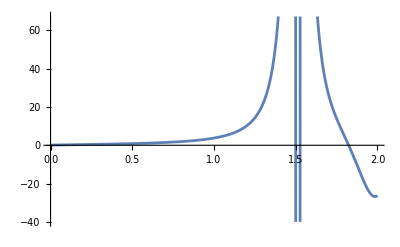

```mathematica
f[t_,y_]:=6 y^2+t
TMax=2;
y0=0.1+0.02I;v0=1.3;
ySol=NDSolveValue[{y''[t]==f[t,y[t]],y[0]==y0,y'[0]==v0},y,{t,0, TMax}]
Plot[Re[ySol[t]],{t,0,TMax}]
```

Search “Does y’’=6y^2+z have a name?” for some background.  Our interest here is the action (without any warnings) near z=3/2. Here is a close up with both the real and imaginary bits.

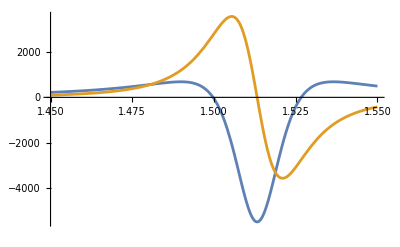

```mathematica
Plot[ {Re[ySol[t]],Im[ySol[t]]},{t,1.45,1.55}]
```

Lets see how big the steps are.  You can take the interpolating function to pieces and see where the dots are.

```mathematica
tVals=Flatten[ySol["Grid"]];
tΔtVals=Table[ 
{tVals⟦i-1⟧+tVals⟦i⟧, tVals⟦i⟧-tVals⟦i-1⟧},
{i, 2, Length[tVals]}];
TabView[{
"t"->ListPlot[tVals,PlotRange->All],
"t vs Δt"->ListPlot[tΔtVals,PlotRange->All],
"t vs Δt (log scale)"->ListLogPlot[tΔtVals,PlotRange->All]
}]
```

123

Not sure if folks know how to interpret these!

```mathematica
ySol["Methods"]
ySol["InterpolationMethod"]
ySol["InterpolationOrder"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

Hermite

{3}

There is a copy of a relatively recent article by Bengt Fornberg on GitHub using what he calls “pole friendly” solvers based on Pade approximants rather than Taylor Series to solve the P_1 ODE accurately.

## Mixed Systems and Software

Mathematica can solve higher order and mixed systems directly.  Most other software will make you rewrite the system as a first order system by introducing new variables for derivatives.  Some software makes you merge variables into a vector.  
All higher order and mixed systems can be written as 1st order systems.  An example makes this clear.

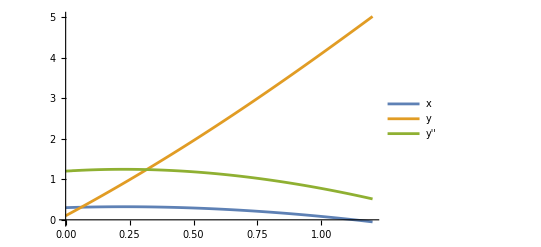

```mathematica
TMax=1.2;
{xSol1, ySol1}=NDSolveValue[{
y'''[t]== x'[t]+ Sin[x'[t]], 
x''[t]==Cos[y'[t]+x'[t]],
y''[0]==1.2,
y'[0]==3.4,
y[0]==0.1,
x'[0]==0.2,
x[0]==0.3},
{x,y},{t, 0, TMax}];
Plot[{xSol1[t],ySol1[t],ySol1''[t]},{t,0, TMax},
PlotLegends->{"x","y","y''"}]
```

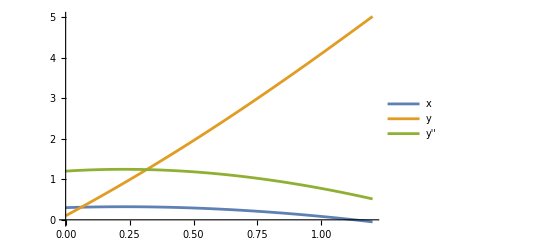

```mathematica
{xSol2,xdSol2, ySol2, ydSol2, yddSol2}=NDSolveValue[{
ydd'[t]== xd[t]+ Sin[xd[t]], 
xd'[t]==Cos[yd[t]+xd[t]],
y'[t]==yd[t],
yd'[t]==ydd[t],
x'[t]==xd[t],
ydd[0]==1.2,
yd[0]==3.4,
y[0]==0.1,
xd[0]==0.2,
x[0]==0.3},
{x,xd,y,yd,ydd},{t, 0, TMax}];
Plot[{xSol2[t],ySol2[t],yddSol2[t]},{t,0, TMax},
PlotLegends->{"x","y","y''"}]
```